```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ]==0,{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[(1/Mαs[Mt,6])αsNf4Loop[Mt,6]-((1/Mαs[Mt,6])αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[Mαs[Mb,5]αsNf4Loop[Mb,4]-(Mαs[Mb,5]αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[Mαs[Mc,4]Mαs[Mb,5]αsNf4Loop[Mc,3]-(Mαs[Mc,4]Mαs[Mb,5]αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[(1/Mαs2Loop[Mt,6])αsNf3Loop[Mt,6]-((1/Mαs2Loop[Mt,6])αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[Mαs2Loop[Mb,5]αsNf3Loop[Mb,4]-(Mαs2Loop[Mb,5]αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Mc,3]-(Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
μoΛTab=1/{.3,.25,.05,.01,.001}
```

{3.33333,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD[4]
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

4.94127

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD[5]
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.0657

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD[6]
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1932.07

1904.31

1860.69

3990.83

```mathematica
nfTab=Table[If[μoΛTab[[n]]>1932,6,If[μoΛTab[[n]]>22,5,If[μoΛTab[[n]]>5,4,3]]],{n,Length[μoΛTab]}]
```

{3,3,4,5,5}

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.378129,0.378129,0.303565,0.213,0.213}

{0.335423,0.335423,0.299152,0.217435,0.217435}

{0.386001,0.386001,0.332194,0.229911,0.229911}

{0.147643,0.147643,0.122648,0.0893248,0.0893248}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{1.26043,1.51252,6.07131,21.3,213.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{1.11808,1.34169,5.98303,21.7435,217.435}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{1.28667,1.544,6.64387,22.9911,229.911}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.492143,0.590571,2.45297,8.93248,89.3248}

```mathematica
α4Tab=Table[{μoΛTab[[n]],αs[μGeVTab[[n]]]},{n,Length[nfTab]}]
```

{{3.33333,0.364226},{4.,0.337729},{20.,0.202298},{100.,0.151919},{1000.,0.105198}}

```mathematica
α3Tab=Table[{μoΛTab[[n]],αs3Loop[μGeV3LoopTab[[n]]]},{n,Length[nfTab]}]
```

{{3.33333,0.429681},{4.,0.373108},{20.,0.204763},{100.,0.152134},{1000.,0.105092}}

```mathematica
α2Tab=Table[{μoΛTab[[n]],αs2Loop[μGeV2LoopTab[[n]]]},{n,Length[nfTab]}]
```

{{3.33333,0.418232},{4.,0.372494},{20.,0.200221},{100.,0.150653},{1000.,0.104287}}

```mathematica
α1Tab=Table[{μoΛTab[[n]],αs1Loop[μGeV1LoopTab[[n]]]},{n,Length[nfTab]}]
```

{{3.33333,0.579857},{4.,0.503596},{20.,0.251685},{100.,0.177962},{1000.,0.118641}}

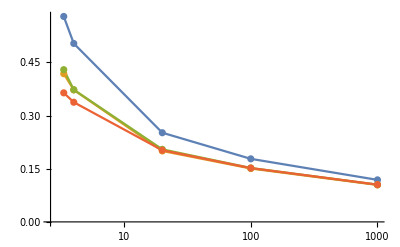

```mathematica
Show[ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},Joined->True],ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab}]]
```

```mathematica
αs[1]
```

0.395109

```mathematica
αs3Loop[1]
```

0.47641

```mathematica
αs2Loop[1]
```

0.545637

```mathematica
αs1Loop[1]
```

0.364949

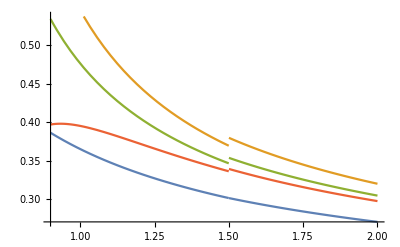

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.9,2}]
```

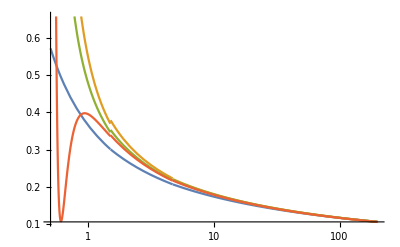

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### Grid

```mathematica
μoΛTab=1/{.3,.25,.2,.19,.18,.17,.16,.15,.14,.13,.12,.11,.1,.09,.08,.07,.06,.05,.025,.01,0.005,.001,.0005}
```

{3.33333,4.,5.,5.26316,5.55556,5.88235,6.25,6.66667,7.14286,7.69231,8.33333,9.09091,10.,11.1111,12.5,14.2857,16.6667,20.,40.,100.,200.,1000.,2000.}

```mathematica
nfTab=Table[If[μoΛTab[[n]]>1932,6,If[μoΛTab[[n]]>22,5,If[μoΛTab[[n]]>5,4,3]]],{n,Length[μoΛTab]}]
```

{3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,6}

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.378129,0.378129,0.378129,0.303565,0.303565,0.303565,0.303565,0.303565,0.303565,0.303565,0.303565,0.303565,0.303565,0.303565,0.303565,0.303565,0.303565,0.303565,0.213,0.213,0.213,0.213,0.0897171}

{0.335423,0.335423,0.335423,0.299152,0.299152,0.299152,0.299152,0.299152,0.299152,0.299152,0.299152,0.299152,0.299152,0.299152,0.299152,0.299152,0.299152,0.299152,0.217435,0.217435,0.217435,0.217435,0.0910249}

{0.386001,0.386001,0.386001,0.332194,0.332194,0.332194,0.332194,0.332194,0.332194,0.332194,0.332194,0.332194,0.332194,0.332194,0.332194,0.332194,0.332194,0.332194,0.229911,0.229911,0.229911,0.229911,0.0931592}

{0.147643,0.147643,0.147643,0.122648,0.122648,0.122648,0.122648,0.122648,0.122648,0.122648,0.122648,0.122648,0.122648,0.122648,0.122648,0.122648,0.122648,0.122648,0.0893248,0.0893248,0.0893248,0.0893248,0.0434346}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{1.26043,1.51252,1.89065,1.59771,1.68647,1.78568,1.89728,2.02377,2.16832,2.33512,2.52971,2.75969,3.03565,3.37295,3.79457,4.33665,5.05942,6.07131,8.52,21.3,42.6,213.,179.434}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{1.11808,1.34169,1.67712,1.57448,1.66195,1.75971,1.8697,1.99434,2.1368,2.30117,2.49293,2.71956,2.99152,3.32391,3.73939,4.27359,4.98586,5.98303,8.69739,21.7435,43.4869,217.435,182.05}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{1.28667,1.544,1.93001,1.74839,1.84552,1.95408,2.07621,2.21462,2.37281,2.55534,2.76828,3.01994,3.32194,3.69104,4.15242,4.74562,5.53656,6.64387,9.19644,22.9911,45.9822,229.911,186.318}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.492143,0.590571,0.738214,0.645518,0.68138,0.721461,0.766553,0.817656,0.87606,0.94345,1.02207,1.11499,1.22648,1.36276,1.53311,1.75212,2.04414,2.45297,3.57299,8.93248,17.865,89.3248,86.8693}

```mathematica
α4Tab=Table[{μoΛTab[[n]],αs[μGeVTab[[n]]]},{n,Length[nfTab]}]
```

{{3.33333,0.364226},{4.,0.337729},{5.,0.304595},{5.26316,0.329014},{5.55556,0.320794},{5.88235,0.312499},{6.25,0.304122},{6.66667,0.295656},{7.14286,0.28709},{7.69231,0.278408},{8.33333,0.269591},{9.09091,0.260611},{10.,0.251436},{11.1111,0.242021},{12.5,0.232304},{14.2857,0.222205},{16.6667,0.21265},{20.,0.202298},{40.,0.185578},{100.,0.151919},{200.,0.133736},{1000.,0.105198},{2000.,0.107423}}

```mathematica
α3Tab=Table[{μoΛTab[[n]],αs3Loop[μGeV3LoopTab[[n]]]},{n,Length[nfTab]}]
```

{{3.33333,0.429681},{4.,0.373108},{5.,0.332484},{5.26316,0.344048},{5.55556,0.334093},{5.88235,0.324243},{6.25,0.314473},{6.66667,0.30476},{7.14286,0.295077},{7.69231,0.285396},{8.33333,0.275684},{9.09091,0.265905},{10.,0.256014},{11.1111,0.245959},{12.5,0.23567},{14.2857,0.225059},{16.6667,0.21543},{20.,0.204763},{40.,0.185974},{100.,0.152134},{200.,0.133884},{1000.,0.105092},{2000.,0.107392}}

```mathematica
α2Tab=Table[{μoΛTab[[n]],αs2Loop[μGeV2LoopTab[[n]]]},{n,Length[nfTab]}]
```

{{3.33333,0.418232},{4.,0.372494},{5.,0.326023},{5.26316,0.344882},{5.55556,0.334266},{5.88235,0.323821},{6.25,0.31352},{6.66667,0.303337},{7.14286,0.293245},{7.69231,0.283213},{8.33333,0.273207},{9.09091,0.263189},{10.,0.253113},{11.1111,0.242926},{12.5,0.232558},{14.2857,0.220326},{16.6667,0.210603},{20.,0.200221},{40.,0.184168},{100.,0.150653},{200.,0.132653},{1000.,0.104287},{2000.,0.106984}}

```mathematica
α1Tab=Table[{μoΛTab[[n]],αs1Loop[μGeV1LoopTab[[n]]]},{n,Length[nfTab]}]
```

{{3.33333,0.579857},{4.,0.503596},{5.,0.433774},{5.26316,0.473227},{5.55556,0.456497},{5.88235,0.44005},{6.25,0.423853},{6.66667,0.407872},{7.14286,0.392068},{7.69231,0.376403},{8.33333,0.360831},{9.09091,0.345302},{10.,0.329757},{11.1111,0.314124},{12.5,0.298521},{14.2857,0.283531},{16.6667,0.267996},{20.,0.251685},{40.,0.223612},{100.,0.177962},{200.,0.15468},{1000.,0.118641},{2000.,0.119122}}

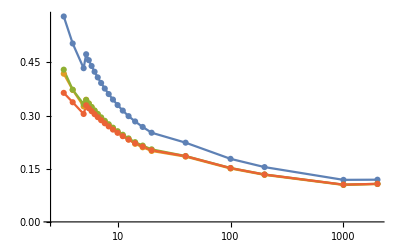

```mathematica
Show[ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},Joined->True],ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab}]]
```

### Charm and above

```mathematica
μoΛTab=1/{.19,.15,.11,.07,.046,.044,.02,.005,.001,.0006,.0005,.0003,.0001,.00003,.00001}
```

{5.26316,6.66667,9.09091,14.2857,21.7391,22.7273,50.,200.,1000.,1666.67,2000.,3333.33,10000.,33333.3,100000.}

```mathematica
nfTab=Table[If[μoΛTab[[n]]>1932,6,If[μoΛTab[[n]]>22,5,If[μoΛTab[[n]]>5,4,3]]],{n,Length[μoΛTab]}]
```

{4,4,4,4,4,5,5,5,5,5,6,6,6,6,6}

```mathematica
Length[nfTab]
```

15

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.303565,0.303565,0.303565,0.303565,0.303565,0.213,0.213,0.213,0.213,0.213,0.0897171,0.0897171,0.0897171,0.0897171,0.0897171}

{0.299152,0.299152,0.299152,0.299152,0.299152,0.217435,0.217435,0.217435,0.217435,0.217435,0.0910249,0.0910249,0.0910249,0.0910249,0.0910249}

{0.332194,0.332194,0.332194,0.332194,0.332194,0.229911,0.229911,0.229911,0.229911,0.229911,0.0931592,0.0931592,0.0931592,0.0931592,0.0931592}

{0.122648,0.122648,0.122648,0.122648,0.122648,0.0893248,0.0893248,0.0893248,0.0893248,0.0893248,0.0434346,0.0434346,0.0434346,0.0434346,0.0434346}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{1.59771,2.02377,2.75969,4.33665,6.59925,4.84091,10.65,42.6,213.,355.,179.434,299.057,897.171,2990.57,8971.71}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{1.57448,1.99434,2.71956,4.27359,6.50329,4.9417,10.8717,43.4869,217.435,362.391,182.05,303.416,910.249,3034.16,9102.49}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{1.74839,2.21462,3.01994,4.74562,7.2216,5.22525,11.4956,45.9822,229.911,383.185,186.318,310.531,931.592,3105.31,9315.92}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.645518,0.817656,1.11499,1.75212,2.66627,2.03011,4.46624,17.865,89.3248,148.875,86.8693,144.782,434.346,1447.82,4343.46}

```mathematica
α4Tab=Table[{μoΛTab[[n]],αs[μGeVTab[[n]]]},{n,Length[nfTab]}]
```

{{5.26316,0.329014},{6.66667,0.295656},{9.09091,0.260611},{14.2857,0.222205},{21.7391,0.197902},{22.7273,0.215323},{50.,0.176037},{200.,0.133736},{1000.,0.105198},{1666.67,0.0990926},{2000.,0.107423},{3333.33,0.101061},{10000.,0.0896678},{33333.3,0.0798339},{100000.,0.0725871}}

```mathematica
α3Tab=Table[{μoΛTab[[n]],αs3Loop[μGeV3LoopTab[[n]]]},{n,Length[nfTab]}]
```

{{5.26316,0.344048},{6.66667,0.30476},{9.09091,0.265905},{14.2857,0.225059},{21.7391,0.200241},{22.7273,0.21598},{50.,0.176372},{200.,0.133884},{1000.,0.105092},{1666.67,0.0990003},{2000.,0.107392},{3333.33,0.101036},{10000.,0.0896503},{33333.3,0.0798207},{100000.,0.0725762}}

```mathematica
α2Tab=Table[{μoΛTab[[n]],αs2Loop[μGeV2LoopTab[[n]]]},{n,Length[nfTab]}]
```

{{5.26316,0.344882},{6.66667,0.303337},{9.09091,0.263189},{14.2857,0.220326},{21.7391,0.195827},{22.7273,0.214144},{50.,0.174633},{200.,0.132653},{1000.,0.104287},{1666.67,0.0982764},{2000.,0.106984},{3333.33,0.100663},{10000.,0.0893431},{33333.3,0.07957},{100000.,0.0723657}}

```mathematica
α1Tab=Table[{μoΛTab[[n]],αs1Loop[μGeV1LoopTab[[n]]]},{n,Length[nfTab]}]
```

{{5.26316,0.473227},{6.66667,0.407872},{9.09091,0.345302},{14.2857,0.283531},{21.7391,0.24487},{22.7273,0.268654},{50.,0.209732},{200.,0.15468},{1000.,0.118641},{1666.67,0.110472},{2000.,0.119122},{3333.33,0.110889},{10000.,0.0974555},{33333.3,0.0861889},{100000.,0.0779644}}

```mathematica
<<MaTeX`
```

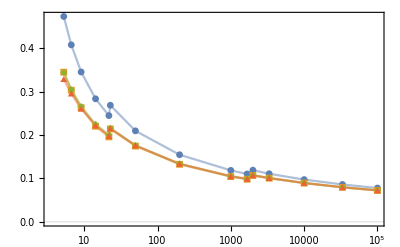

```mathematica
Show[ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotStyle->{Opacity[.5]},Joined->True],ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotMarkers->{Automatic, Small}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\mu/\\Lambda_{QCD}",Magnification->1.2],MaTeX["\\alpha_s(\\mu/\\Lambda_{QCD})",Magnification->1.2]}]
```